This notebook implements numerical calculations from the 2025 musmat-article
“Unified musical quantum models for tonal attraction” by Peter beim Graben and Thomas Noll
https://musmat.org/journal/v9/01-beim-Graben-Noll.pdf
The results are formated for export and usage in a companion Max/MSP patch.

```mathematica
ClearAll
```

ClearAll

A normalized Gaussian nu with mean mean and variance sigma^2
a Gaussian Mixture from three components (cf. equations (2) and (1) of the musmat-article)

```mathematica
nu[sigma_,mean_][x_]:=1/Sqrt[2 Pi sigma^2]Exp[-1/2 ((x-mean)/sigma)^2]
pMix[sigma_][{a_,b_,c_,alpha_,beta_,gamma_}][x_]:=alpha nu[sigma,a][x]+beta nu[sigma,b][x]+gamma nu[sigma,c][x]
```

In our key example, the three mean values a, b, c and coefficients alpha, beta, gamma and the deviation sigma are as follows: (c.f. plot in Figure 4a of the article and the text below it)

```mathematica
sigma=Pi /(6 Sqrt[2 Log[2]])//N
a=0 (Pi/6)
b=1 (Pi/6)
c=4(Pi/6)
alpha = 0.4874675571530851
beta =0.2035869120568771
gamma= 1-alpha-beta
```

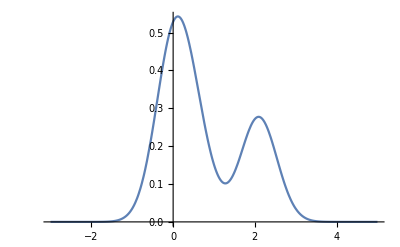

```mathematica
Plot[pMix[sigma][{a,b,c,alpha,beta,gamma}][x],{x,-3, 5}]
```

The next cell calculates the Interaction Potential V[x] as the sum of the Oscillator Potential V0[x] and the Perturbation W[x] (c.f. equations 27, 13, 28 in the musmat article as well as Figure 5.)

```mathematica
E0 = 36 Log[2]/(Pi^2)//N;
V0[x_]:=E0^2x^2
rho[x_]:=Sqrt[E0/Pi]Exp[-E0 x^2]
W[x_]:=
E0^2/(
alpha^2 rho[x-a]^2 + beta^2 rho[x-b]^2+gamma^2 rho[x-c]^2
+2alpha beta rho[x-a]rho[x-b] 
+2alpha gamma rho[x-a]rho[x-c]
+2 beta gamma rho[x-b]rho[x-c]
)(
(a^2-2a x)alpha^2  rho[x-a]^2
+(b^2-2b x)beta^2  rho[x-b]^2
+(c^2-2c x)gamma^2  rho[x-c]^2
+((a-3 b)x+b(2b-a))alpha beta rho[x-a]rho[x-b]
+((b-3 a)x+a(2a-b))alpha beta rho[x-a]rho[x-b]
+((a-3 c)x+c(2c-a))alpha gamma rho[x-a]rho[x-c]
+((c-3 a)x+a(2a-c))alpha gamma rho[x-a]rho[x-c]
+((b-3 c)x+c(2c-b))beta gamma rho[x-b]rho[x-c]
+((c-3 b)x+b(2b-c))beta gamma rho[x-b]rho[x-c]
)
V[x_] := V0[x]+W[x]
```

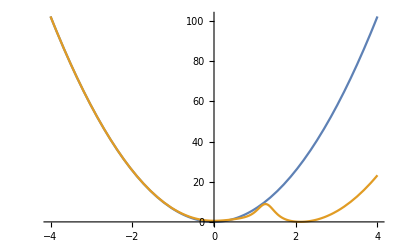

```mathematica
Plot[{V0[x],V[x]},{x,-4, 4}]
```

The following cell defines the normalised Hermite-functions  phi[m_][x_], which form an orthonormal Eigenbasis for the Harmonic oscillator. And we follow equation (35) in order to express the eigenstates of the perturbated oscillator with respect to this basis. With (37) we use them together with the pertubation potential W[x] to numerically calculate entries of the potentially infinite-dimensional matrix w_nm. The integrand for these calulations is w[n_][m_][x_]

```mathematica
phi[m_][x_]:=(E0^(1/4)HermiteH[m,√E0 x] ⅇ^(-(E0 x^2)/2))/(√(2^m m! √π))

w[n_][m_][x_]:=phi[n][x]W[x] phi[m][x]
```

We choose a dimension dim+1 for a finite-dimensional approximation as well as a finite domain (xmin, xmax) for the integration. The numerically integrated coefficients are then stored in a matrix dnm = enm + wnm.

```mathematica
dim=30
xmin=-10
xmax=10
wnm=Table[NIntegrate[w[n][m][x],{x,xmin,xmax}]//N,{n,0,dim},{m,0,dim}];
enm=Table[(2 E0 n +E0)KroneckerDelta[n,m],{n,0,dim},{m,0,dim}];
dnm=enm+wnm;
```

30

-10

10

Next we calculate the Eigensystem of the matrix dnm. Mathematica lists the Eigensystem of a matrix in the descending order of the eigenvalues. But in the case of a Hamiltonian we want them in ascending order. 
The resulting numerically approximated eigenstates EigenState[r_][x_] are still continuous functions on the real axis.

```mathematica
EigenvalueList=Reverse[Eigenvalues[dnm]];
EigenvectorList=Reverse[Eigenvectors[dnm]];
EigenState[r_][x_]:=Plus@@Table[EigenvectorList[[(r+1)]][[l+1]]phi[l][x],{l,0,dim}]
```

```mathematica
The real Eigenvalues and selected values of the (real-valued) stationary Eigenstates are exported into a textfile in the format for Max/MSP coll-file objects with dim+1 lines. For each NotesEigenState we choose 17 points x = k Pi/6 for k = -6, ..., 10 along the x-axis, representing the notes Gb, ...., A#. To each of these lists we prepend the corresponding eigenvalue. Thus, Each line of the collfile  starts with the index m and a comma, and is followed by the Eigenvalue of index m, the NotesEigenState of index m and a semicolon.
```

```mathematica
ThomasRound[x_]:=Round[100000 * x]/100000//N

NotesEigenState[m_]:=ThomasRound/@Prepend[Table[EigenState[m][k Pi/6],{k,-6,10}],EigenvalueList[[m+1]]]

Math2Coll[m_][X_]:=OutputForm[ToString[m]<>", "<>StringReplace[ToString[X],{"{"->"","}"->"", ","->" "}]<>";"]

SetDirectory["/Users/thomas/Documents/Arbeit 2026/Palermo Proceedings/Final Submission/Examples"]

Schreib = OpenWrite["EigenSystem_C_Major.txt",PageWidth->Infinity]
Do[Write[Schreib,Math2Coll[m][NotesEigenState[m]]],{m,0,dim}]
Close[Schreib]
```

For a given initial state (defined as a continuous function InitialState[x] on R) we obtain its dim+1 coefficients with respect to the Eigenstate-Basis as follows:
As an example we use the deflected ground state by k fifths: 
InitialState[x_] = EigenState[0][x-shift] for shift = k Pi/6
For the numerical Integration it is important to include "?NumericQ" into the definition of InitialState[x_]

```mathematica
k=1
shift = k Pi/6
InitialState[x_?NumericQ]:=EigenState[0][x-shift]

CalculateCoefficients[f_]:=Table[NIntegrate[f[x]*EigenState[r][x],{x,xmin,xmax}],{r,0,dim}]
TheseCoefficients = AbsArg/@CalculateCoefficients[InitialState]
```

1

π/6

{{0.902023,0},{0.150004,π},{0.222113,0},{0.255354,0},{0.206996,0},{0.0577094,0},{0.034299,π},{0.00951694,0},{0.0293439,0},{0.0201182,0},{0.0116989,0},{0.0147933,0},{0.0048983,0},{0.0110694,0},{0.000167349,π},{0.00736697,π},{0.00331887,0},{0.00286429,π},{0.00406116,π},{0.00135382,π},{0.00127862,0},{0.00198638,π},{0.00127727,π},{0.000223954,π},{0.000516414,π},{0.000797001,0},{0.000721411,π},{0.000510373,0},{0.000187106,0},{0.0000219351,0},{0.000063036,π}}

```mathematica
SetDirectory["/Users/thomas/Documents/Arbeit 2026/Palermo Proceedings/Final Submission/Examples"]
Schreib = OpenWrite["InitialStateCoefficients_ShiftedGroundState_1Fifth.txt",PageWidth->Infinity]
Do[Write[Schreib,Math2Coll[m][ThomasRound/@TheseCoefficients[[m+1]]]],{m,0,dim}]
Close[Schreib]
```

/Users/thomas/Documents/Arbeit 2026/Palermo Proceedings/Final Submission/Examples

OutputStream[…]

InitialStateCoefficients_ShiftedGroundState_1Fifth.txt

```mathematica
SystemOpen["InitialStateCoefficients_ShiftedGroundState_1Fifth.txt"]
```

```mathematica
SystemOpen["InitialStateCoefficients_ShiftedGroundState_1Fifth.txt"]
```

```mathematica
SystemOpen["EigenSystem_C_Major.txt"]
```

```mathematica
SystemOpen["EigenSystem_C_Major.txt"]
```

```mathematica
SystemOpen["EigenSystem_C_Major.txt"]
```

```mathematica
EigenvalueList
```

{2.5283,3.0726,6.99565,9.18209,12.6457,15.872,19.342,23.0158,26.6294,30.5037,34.2703,38.2667,42.2012,46.3621,50.5755,55.0932,59.8065,64.7675,69.958,75.3575,81.0449,87.0194,93.2473,99.7095,106.383,113.239,120.247,127.374,134.588,141.875,149.308}

```mathematica
NotesEigenState[0]
```

{2.5283,-0.0000209524,0.000120587,0.00260802,0.0293039,0.16643,0.479678,0.727065,0.633832,0.368549,0.388292,0.526774,0.372228,0.131558,0.0232418,0.00209937,0.0000482103,-9.03209×10^-6}